```mathematica
SetDirectory[NotebookDirectory[]];
mat2 = Import["Displacements.txt","Table"];
```

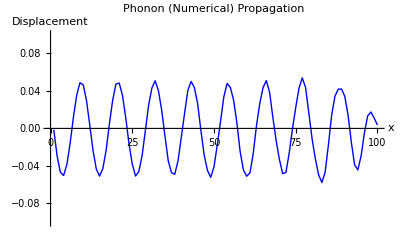

```mathematica
ListPlot[{mat2[[All,370]]},Joined->True,PlotRange-> {-0.1,0.1}, PlotStyle-> Blue,AxesLabel-> {x,Displacement},PlotLabel->"Phonon (Numerical) Propagation"]
```

```mathematica
(*Frequency applied w=2. Wave number calculated from the dispersion relation*)
```

```mathematica
usmall[z_] := 0.05Cos[√0.3 z]
```

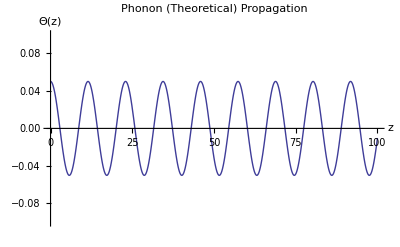

```mathematica
Plot[usmall[z],{z,0,100},PlotRange-> {-0.1,0.1}, PlotLabel->"Phonon (Theoretical) Propagation", AxesLabel-> {z,Θ[z]}]
```

```mathematica
utheory = Table[usmall[i],{i,1,100}];
```

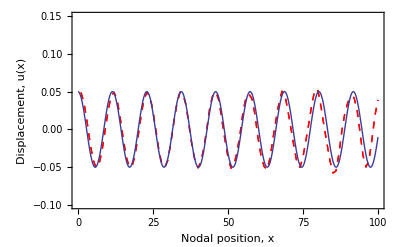

```mathematica
Show[ListPlot[{mat2[[All,377]],mat2[[All,377]]},Joined->True,PlotRange-> {-0.1,0.15}, AspectRatio->1/GoldenRatio,PlotStyle-> Directive[Red,Dashed,Thick],Frame->True,PlotLegends->Placed[LineLegend[{"Numerical Result"}],{Right,Top}]],Plot[usmall[z],{z,0,100},PlotRange-> {-0.13,0.13},AspectRatio->1/GoldenRatio,PlotLegends->Placed[{"Theoretical Result"},{Right,Top}],Frame->True],FrameLabel->{"Nodal position, x","Displacement, u(x)"},BaseStyle->{FontFamily->"Times",14}]
```

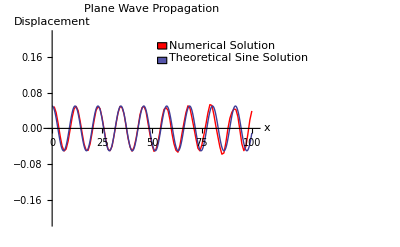

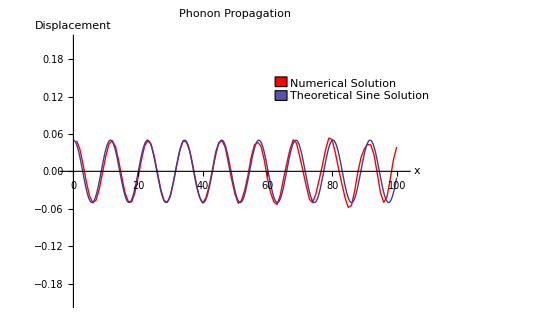

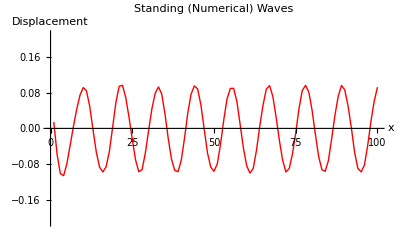

```mathematica
ListPlot[mat2[[All,780]],PlotJoined->True,PlotRange-> {-0.21,0.21}, PlotStyle-> Red,AxesLabel-> {x,Displacement},PlotLabel->"Standing (Numerical) Waves"]
```

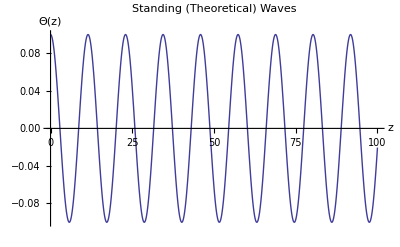

```mathematica
Plot[2usmall[z],{z,0,100},PlotRange-> {-0.1,0.1}, PlotLabel->"Standing (Theoretical) Waves", AxesLabel-> {z,Θ[z]}]
```

```mathematica
Show[ListPlot[mat2[[All,780]],PlotJoined->True,PlotRange-> {-0.21,0.21}, PlotStyle-> Red,AxesLabel-> {x,Displacement},PlotLabel->"Standing Waves"],Plot[2usmall[z-10],{z,0,100},PlotRange-> {-0.1,0.1}, PlotLabel->"Sine Gordon Soliton Propagation", AxesLabel-> {z,Θ[z]}]]
```

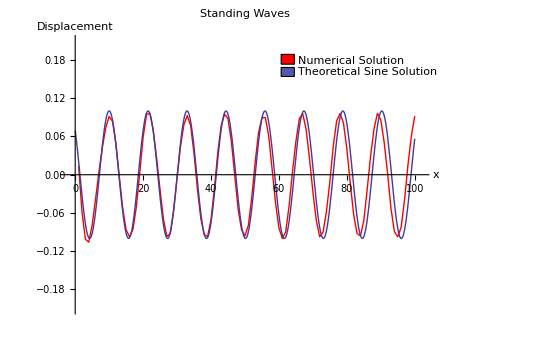

```mathematica
plots = Table[ListPlot[mat2[[All,i]],PlotJoined->True,PlotRange-> {-0.35,0.35},AxesLabel-> {x,Displacement},PlotLabel->"Phonon (Numerical) Propagation"],{i,1,1000}];
ListAnimate[plots]
```

```mathematica
Export["small_amplitude_animation.avi",plots]
```

small_amplitude_animation.avi

```mathematica
fourierplots = Table[ListPlot[Abs[Fourier[mat2[[All,i]]]],Joined->True,PlotRange-> {-0.35,0.35}],{i,1,300}];
```

```mathematica
ListAnimate[fourierplots]
```

```mathematica
Needs["PlotLegends`"]
```

```mathematica
mat3 = Table[mat2[[All,i]],{i,1,370}];
```

```mathematica
A = ListContourPlot[mat3, FrameLabel->{"Position, x^-","Time , t^-"},PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->20}],BaseStyle->{FontFamily->"Times",20},AspectRatio->1]
```

-Graphics-

```mathematica
v = 0.2/√0.3;
```

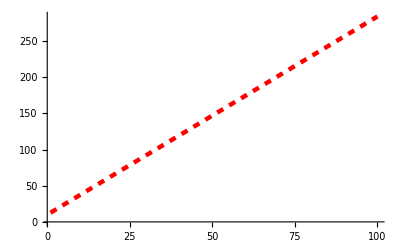

```mathematica
B = Plot[x/v+10,{x,1,100},PlotStyle-> {Red,Thickness[0.008],Dashed}]
```

```mathematica
image = Show[A,B]
```

-Graphics-

```mathematica
Export["smallContour.pdf",image]
```

smallContour.pdf